# Average IPR vs Jz

.9f Description
The Inverse Participation Ratio (IPR) of each eigenstate measures how much spread it is in a particular basis. A high value of IPR means that the eigenstate is spread out in that basis, while a low value of IPR means that the state is more localized.                                                                   Here we choose the site-basis and compute the average value of the IPR’s of all eigenstates for each value of Jz. (The code provided here is used to obtain the bottom of Figure 1 in the paper)

.9f Notation
*) IPR = Inverse Participation Ratio
*) AveIPR = average value of IPR for all eigenstates

.9f Code for IPR vs Jz

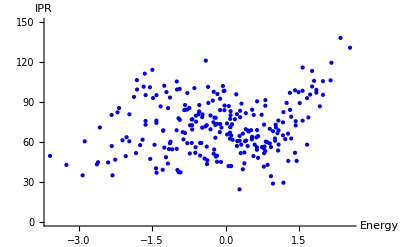

```mathematica
(*Parameters of the Hamiltonian*)
Clear[chainsize,upspins,downspins,dim,Jxy,Jz,open];
chainsize=10;
upspins=chainsize/2;
downspins=chainsize-upspins;
dim=chainsize!/(upspins!downspins!);
Jxy=1.0;
Jz=0.5;
open=1;
(*Creating the basis*)
Clear[onebasisvector,basis];
onebasisvector=Flatten[{Table[1,{k,1,upspins}],Table[0,{k,1,downspins}]}];
basis=Permutations[onebasisvector];

(*ELEMENTS OF THE HAMILTONIAN*)
(*Initialization*)
Clear[HH];
Do[Do[HH[i,j]=0.,{j,1,dim}],{i,1,dim}];

(*Diagonal elements-Ising interaction*)
Do[
Do[
HH[i,i]=HH[i,i]+(Jz/4.)*(-1.)^(basis[[i,k]]+basis[[i,k+1]]);
       ,{k,1,chainsize-1}];
,{i,1,dim}];
(*Term included in the Ising interaction if the chain is closed*)
If[open==0,
Do[HH[i,i]=HH[i,i]+(Jz/4.)*(-1.)^(basis[[i,chainsize]]+basis[[i,1]]),
{i,1,dim}]];

(*Off-diagonal elements-flip-flop term*)
Clear[howmany,site];
Do[
Do[
(*Initialization*)
howmany=0
Do[site[z]=0,{z,1,chainsize}];
(*Sites where states i and j differ*)
Do[If[basis[[i,k]]≠basis[[j,k]],{howmany=howmany+1,site[howmany]=k}];,{k,1,chainsize}];
(*Coupling matrix element-when only two neighbor sites differ*)
If[howmany==2,If[site[2]-site[1]==1,{HH[i,j]=HH[i,j]+Jxy/2.,HH[j,i]=HH[j,i]+Jxy/2.}]];
(*Additional term for closed system*)If[open==0, If[site[2]-site[1]==chainsize-1,{HH[i,j]=HH[i,j]+Jxy/2.,HH[j,i]=HH[j,i]+Jxy/2.}]];
,{j,i+1,dim}];
,{i,1,dim-1}];

(* TOTAL HAMILTONIAN AND DIAGONALIZATION *)
Clear[Hamiltonian,Energy,Vector];
Hamiltonian=Table[Table[HH[i,j],{j,1,dim}],{i,dim}];
Energy=Eigenvalues[Hamiltonian];
Vector=Eigenvectors[Hamiltonian];

(*Inverse Participation Ratio:IPR*)

Clear[IPR];
Do[
IPR[i]=1/Sum[Vector[[i,k]]^4,{k,1,dim}];
,{i,1,dim}];

(*Plot:IPR vs Jz*)
Clear[tab];
tab=Table[{Energy[[j]],IPR[j]},{j,1,dim}];
ListPlot[tab, LabelStyle->Directive[Black,Bold,Medium],PlotStyle->Blue,AxesLabel->{"Energy","IPR"}, PlotRange->{0,150}]
```